```mathematica
PrependTo[$Path,"/Users/annils14/Documents/KerrModes"];PrependTo[$Path,"~/Research/KerrQNM/KerrModes"];
Needs["KerrTTML`"]
SetSpinWeight[-2]
SelectMode[PolynomialMode]
```

All KerrMode routines (TTML) set for Spin-Weight s = -2

Mode set to find Polynomial solutions

```mathematica
SchTTMLTable[2]=2;
SchTTMLTable[2,0]={-2.00*I,0,0,0,0};
SchTTMLTable[2,1]={-2.00*I,0,0,0,0};
SchTTMLTable[3]=2;
SchTTMLTable[3,0]={-10.0*I,0,0,0,0};
SchTTMLTable[3,1]={-10.0*I,0,0,0,0};
```

```mathematica
SchwarzschildTTML[2,0]
```

Computing (l=2,n=0)

{-2. ⅈ,0,300,-14,0}

```mathematica
SchwarzschildTTML[3,0]
```

Computing (l=3,n=0)

{-10. ⅈ,0,300,-14,0}

```mathematica
KerrTTMLSequence[2,0,0,-8,SeqDirection->Forward]
```

KerrModes`Private`KerrModeSequence::solfail: a+/- solution failed.

$Aborted

```mathematica
N[KerrTTML[2,0,{0,0}][[-1,1]]]
```

0.493375

```mathematica
KerrModeMakeMultiplet[2,0,0]
```

```mathematica
Show[ModePlotOmega[2,0,{0,0}],ModePlotOmega[2,0,{0,1}],PlotRange->All]
```

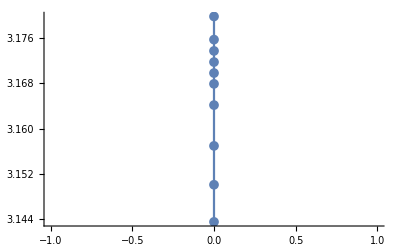

```mathematica
ListLinePlot[Chop[Take[KerrOmegaList[2,0,{0,0}],-10]],PlotRange->Automatic,PlotMarkers->{Automatic, 10}]
```

-Graphics-

```mathematica
ShortenModeSequence[2,0,{0,1},1]
```

Original Length of KerrQNM[2,0,{0,1}]=117

Removing first 1 elements

```mathematica
<<"~/Research/KerrQNM/KerrModes/TTMLmodes.dat";
```

```mathematica
<<"~/Research/KerrQNM/KerrModes/QNMmodes.dat";
```

```mathematica
t=Null[]
```

Null[]

```mathematica
MemberQ[{QNM,TTML,TTMR},QNM]
```

True

```mathematica
QNM!=Null[]
```

QNM≠Null[]

Debug 0 : ModeType->Null[]

Debug 1 : ModeType->Null[]

Debug 0 : ModeType->Null[]

Debug 1 : ModeType->Null[]

Debug 0 : ModeType->QNM

Debug 1 : ModeType->QNM

Debug 2 :

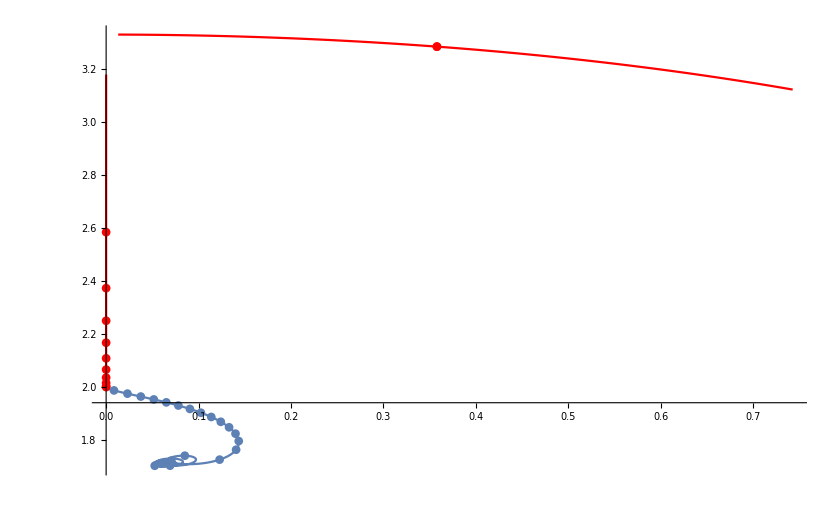

```mathematica
Show[ModePlotOmega[2,0,{0,0},PlotStyle->Red],ModePlotOmega[2,0,{0,1},PlotStyle->Red],ModePlotOmega[2,0,{8,0},ModeType->QNM],PlotRange->All]
```

```mathematica
?ShortenModeSequence
```

ShortenModeSequence[l,m,n,N] removes the first N elements of the Mode sequence (l,m,n)
if N>0, and removes the last N elements if N<0.

Options:
	 ShortenBy→Drop : Drop, Take
		 If 'Take' is chosen, the first N elemets are kept if N>0, and the last N elements
		 are kept if N<0.

```mathematica
KerrTTMLSequence[2,0,{0,1},-8,SeqDirection->Backward,ModeaStart->{51/100,0.578-3.21ⅈ,4}]
```

Set $MinPrecision = 24

KerrTTML[2,0,{0,1}] sequence exists with 23 entries

ModeSol a=0.5095 ω=0.575402-3.21005 ⅈ Alm=5.27212+0.428421 ⅈ

ModeSol a=0.509 ω=0.56647-3.21393 ⅈ Alm=5.27346+0.421333 ⅈ

ModeSol a=0.5085 ω=0.557348-3.21781 ⅈ Alm=5.2748+0.414118 ⅈ

ModeSol a=0.508 ω=0.548026-3.22171 ⅈ Alm=5.27614+0.406769 ⅈ

ModeSol+ a=0.50875 ω=0.561933-3.21587 ⅈ Alm=5.27413+0.417742 ⅈ

ModeSol- a=0.50825 ω=0.552713-3.21976 ⅈ Alm=5.27547+0.410461 ⅈ

Decreasing Δa, blevel = 2

ModeSol a=0.50775 ω=0.543288-3.22366 ⅈ Alm=5.27681+0.403042 ⅈ

ModeSol a=0.5075 ω=0.538495-3.22562 ⅈ Alm=5.27748+0.399278 ⅈ

ModeSol a=0.50725 ω=0.533647-3.22757 ⅈ Alm=5.27815+0.395478 ⅈ

ModeSol a=0.507 ω=0.528741-3.22953 ⅈ Alm=5.27882+0.391638 ⅈ

ModeSol a=0.50675 ω=0.523778-3.23149 ⅈ Alm=5.27949+0.387759 ⅈ

ModeSol a=0.5065 ω=0.518753-3.23346 ⅈ Alm=5.28016+0.383839 ⅈ

ModeSol a=0.50625 ω=0.513667-3.23542 ⅈ Alm=5.28083+0.379878 ⅈ

ModeSol a=0.506 ω=0.508517-3.23739 ⅈ Alm=5.2815+0.375872 ⅈ

ModeSol a=0.50575 ω=0.5033-3.23936 ⅈ Alm=5.28217+0.371822 ⅈ

ModeSol a=0.5055 ω=0.498016-3.24133 ⅈ Alm=5.28284+0.367726 ⅈ

ModeSol a=0.50525 ω=0.492661-3.2433 ⅈ Alm=5.28351+0.363582 ⅈ

ModeSol a=0.505 ω=0.487233-3.24528 ⅈ Alm=5.28419+0.359388 ⅈ

ModeSol a=0.50475 ω=0.48173-3.24726 ⅈ Alm=5.28486+0.355143 ⅈ

ModeSol a=0.5045 ω=0.476149-3.24924 ⅈ Alm=5.28553+0.350844 ⅈ

ModeSol a=0.50425 ω=0.470487-3.25122 ⅈ Alm=5.2862+0.346491 ⅈ

ModeSol a=0.504 ω=0.464742-3.25321 ⅈ Alm=5.28688+0.34208 ⅈ

ModeSol a=0.50375 ω=0.45891-3.25519 ⅈ Alm=5.28755+0.33761 ⅈ

ModeSol a=0.5035 ω=0.452987-3.25718 ⅈ Alm=5.28822+0.333078 ⅈ

ModeSol a=0.50325 ω=0.446971-3.25918 ⅈ Alm=5.2889+0.328482 ⅈ

ModeSol a=0.503 ω=0.440856-3.26117 ⅈ Alm=5.28957+0.323818 ⅈ

ModeSol a=0.50275 ω=0.43464-3.26317 ⅈ Alm=5.29024+0.319085 ⅈ

ModeSol a=0.5025 ω=0.428317-3.26517 ⅈ Alm=5.29092+0.314278 ⅈ

ModeSol a=0.50225 ω=0.421883-3.26717 ⅈ Alm=5.29159+0.309394 ⅈ

ModeSol a=0.502 ω=0.415333-3.26917 ⅈ Alm=5.29227+0.30443 ⅈ

ModeSol a=0.50175 ω=0.40866-3.27118 ⅈ Alm=5.29294+0.299381 ⅈ

ModeSol a=0.5015 ω=0.40186-3.27319 ⅈ Alm=5.29362+0.294244 ⅈ

ModeSol a=0.50125 ω=0.394924-3.2752 ⅈ Alm=5.29429+0.289013 ⅈ

ModeSol a=0.501 ω=0.387846-3.27721 ⅈ Alm=5.29497+0.283683 ⅈ

ModeSol a=0.50075 ω=0.380618-3.27922 ⅈ Alm=5.29564+0.278249 ⅈ

ModeSol a=0.5005 ω=0.37323-3.28124 ⅈ Alm=5.29632+0.272705 ⅈ

ModeSol a=0.50025 ω=0.365674-3.28326 ⅈ Alm=5.297+0.267043 ⅈ

ModeSol a=0.5 ω=0.357939-3.28528 ⅈ Alm=5.29767+0.261256 ⅈ

ModeSol a=0.49975 ω=0.350012-3.28731 ⅈ Alm=5.29835+0.255335 ⅈ

ModeSol a=0.4995 ω=0.341881-3.28933 ⅈ Alm=5.29903+0.249271 ⅈ

ModeSol a=0.49925 ω=0.333529-3.29136 ⅈ Alm=5.2997+0.243053 ⅈ

ModeSol a=0.499 ω=0.324941-3.29339 ⅈ Alm=5.30038+0.23667 ⅈ

ModeSol a=0.49875 ω=0.316097-3.29543 ⅈ Alm=5.30106+0.230106 ⅈ

ModeSol a=0.4985 ω=0.306975-3.29746 ⅈ Alm=5.30174+0.223347 ⅈ

ModeSol a=0.49825 ω=0.297548-3.2995 ⅈ Alm=5.30242+0.216373 ⅈ

ModeSol a=0.498 ω=0.287788-3.30154 ⅈ Alm=5.30309+0.209165 ⅈ

ModeSol a=0.49775 ω=0.277658-3.30359 ⅈ Alm=5.30377+0.201695 ⅈ

ModeSol+ a=0.498125 ω=0.292712-3.30052 ⅈ Alm=5.30275+0.2128 ⅈ

ModeSol- a=0.497875 ω=0.282771-3.30256 ⅈ Alm=5.30343+0.205464 ⅈ

Decreasing Δa, blevel = 3

ModeSol a=0.497625 ω=0.272442-3.30461 ⅈ Alm=5.30411+0.197854 ⅈ

ModeSol a=0.4975 ω=0.267117-3.30563 ⅈ Alm=5.30445+0.193935 ⅈ

ModeSol a=0.497375 ω=0.261677-3.30665 ⅈ Alm=5.30479+0.189935 ⅈ

ModeSol a=0.49725 ω=0.256114-3.30768 ⅈ Alm=5.30513+0.185847 ⅈ

ModeSol a=0.497125 ω=0.25042-3.3087 ⅈ Alm=5.30547+0.181667 ⅈ

ModeSol a=0.497 ω=0.244586-3.30973 ⅈ Alm=5.30581+0.177388 ⅈ

ModeSol a=0.496875 ω=0.238602-3.31076 ⅈ Alm=5.30615+0.173002 ⅈ

ModeSol a=0.49675 ω=0.232456-3.31178 ⅈ Alm=5.30649+0.168501 ⅈ

ModeSol a=0.496625 ω=0.226134-3.31281 ⅈ Alm=5.30683+0.163875 ⅈ

ModeSol a=0.4965 ω=0.219622-3.31384 ⅈ Alm=5.30717+0.159113 ⅈ

ModeSol a=0.496375 ω=0.212903-3.31486 ⅈ Alm=5.30751+0.154204 ⅈ

ModeSol a=0.49625 ω=0.205955-3.31589 ⅈ Alm=5.30785+0.149132 ⅈ

ModeSol a=0.496125 ω=0.198755-3.31692 ⅈ Alm=5.30819+0.14388 ⅈ

ModeSol a=0.496 ω=0.191275-3.31795 ⅈ Alm=5.30853+0.138428 ⅈ

ModeSol a=0.495875 ω=0.18348-3.31898 ⅈ Alm=5.30887+0.132752 ⅈ

ModeSol a=0.49575 ω=0.175328-3.32002 ⅈ Alm=5.30921+0.126819 ⅈ

ModeSol a=0.495625 ω=0.166766-3.32105 ⅈ Alm=5.30955+0.120595 ⅈ

ModeSol a=0.4955 ω=0.157729-3.32208 ⅈ Alm=5.30989+0.114029 ⅈ

ModeSol a=0.495375 ω=0.148129-3.32311 ⅈ Alm=5.31023+0.10706 ⅈ

ModeSol a=0.49525 ω=0.137848-3.32415 ⅈ Alm=5.31057+0.0996029 ⅈ

ModeSol+ a=0.4954375 ω=0.153006-3.3226 ⅈ Alm=5.31006+0.1106 ⅈ

ModeSol- a=0.4953125 ω=0.143082-3.32363 ⅈ Alm=5.3104+0.103399 ⅈ

Decreasing Δa, blevel = 4

ModeSol a=0.4951875 ω=0.132403-3.32466 ⅈ Alm=5.31074+0.0956559 ⅈ

ModeSol a=0.495125 ω=0.126721-3.32518 ⅈ Alm=5.31091+0.0915385 ⅈ

ModeSol a=0.4950625 ω=0.120768-3.3257 ⅈ Alm=5.31108+0.0872265 ⅈ

ModeSol a=0.495 ω=0.114501-3.32622 ⅈ Alm=5.31125+0.0826895 ⅈ

ModeSol a=0.4949375 ω=0.107867-3.32673 ⅈ Alm=5.31142+0.077888 ⅈ

ModeSol a=0.494875 ω=0.100792-3.32725 ⅈ Alm=5.31159+0.07277 ⅈ

ModeSol a=0.4948125 ω=0.0931772-3.32777 ⅈ Alm=5.31176+0.0672629 ⅈ

ModeSol a=0.49475 ω=0.0848759-3.32829 ⅈ Alm=5.31193+0.0612622 ⅈ

ModeSol a=0.4946875 ω=0.0756631-3.32881 ⅈ Alm=5.3121+0.0546052 ⅈ

ModeSol a=0.494625 ω=0.0651532-3.32932 ⅈ Alm=5.31227+0.0470141 ⅈ

ModeSol+ a=0.49471875 ω=0.0804023-3.32855 ⅈ Alm=5.31202+0.0580294 ⅈ

ModeSol- a=0.49465625 ω=0.0706048-3.32906 ⅈ Alm=5.31219+0.0509513 ⅈ

Decreasing Δa, blevel = 5

ModeSol a=0.49459375 ω=0.0591997-3.32958 ⅈ Alm=5.31236+0.0427152 ⅈ

ModeSol a=0.4945625 ω=0.052574-3.32984 ⅈ Alm=5.31244+0.037932 ⅈ

ModeSol a=0.49453125 ω=0.0449802-3.3301 ⅈ Alm=5.31253+0.0324508 ⅈ

ModeSol a=0.4945 ω=0.0358073-3.33036 ⅈ Alm=5.31262+0.0258314 ⅈ

ModeSol a=0.49446875 ω=0.0232568-3.33062 ⅈ Alm=5.3127+0.0167763 ⅈ

ModeSol+ a=0.494515625 ω=0.0406537-3.33023 ⅈ Alm=5.31257+0.0293285 ⅈ

ModeSol- a=0.494484375 ω=0.0301919-3.33049 ⅈ Alm=5.31266+0.0217797 ⅈ

Decreasing Δa, blevel = 6

ModeSol a=0.494453125 ω=0.0130439-3.33075 ⅈ Alm=5.31274+0.00940894 ⅈ

ModeSol+ a=0.4944765625 ω=0.0269485-3.33056 ⅈ Alm=5.31268+0.0194397 ⅈ

ModeSol- a=0.4944609375 ω=0.0188552-3.33069 ⅈ Alm=5.31272+0.013601 ⅈ

Decreasing Δa, blevel = 7

ModeSol a=0.4944453125 ω=-6.81858×10^-27-3.32691 ⅈ Alm=5.30995-4.91476×10^-27 ⅈ

ModeSol+ a=0.49445703125 ω=0.0162121-3.33072 ⅈ Alm=5.31273+0.0116943 ⅈ

ModeSol- a=0.49444921875 ω=0.00880065-3.33078 ⅈ Alm=5.31275+0.00634809 ⅈ

ModeSol+ a=0.494451171875 ω=0.0111265-3.33077 ⅈ Alm=5.31275+0.00802578 ⅈ

ModeSol- a=0.494447265625 ω=0.00557707-3.3308 ⅈ Alm=5.31276+0.00402284 ⅈ

ModeSol+ a=0.4944482421875 ω=0.00736734-3.33079 ⅈ Alm=5.31276+0.0053142 ⅈ

ModeSol- a=0.4944462890625 ω=0.00281594-3.33081 ⅈ Alm=5.31276+0.00203118 ⅈ

ModeSol+ a=0.49444677734375 ω=0.00441776-3.3308 ⅈ Alm=5.31276+0.00318661 ⅈ

ModeSol- a=0.49444580078125 ω=-6.5073×10^-26-3.3289 ⅈ Alm=5.31138-4.69214×10^-26 ⅈ

ModeSol+ a=0.494446044921875 ω=0.00146148-3.33081 ⅈ Alm=5.31276+0.00105419 ⅈ

ModeSol+ a=0.4944461669921875 ω=0.00224337-3.33081 ⅈ Alm=5.31276+0.00161818 ⅈ

ModeSol- a=0.4944459228515625 ω=-4.03946×10^-26-3.32994 ⅈ Alm=5.31213-2.91325×10^-26 ⅈ

ModeSol+ a=0.49444598388671875 ω=0.000829172-3.33081 ⅈ Alm=5.31276+0.000598095 ⅈ

ModeSol+ a=0.494446014404296875 ω=0.00118816-3.33081 ⅈ Alm=5.31276+0.00085704 ⅈ

ModeSol- a=0.494445953369140625 ω=-2.74886×10^-26-3.33062 ⅈ Alm=5.31262-1.98272×10^-26 ⅈ

ModeSol+ a=0.4944459686279296875 ω=0.000570462-3.33081 ⅈ Alm=5.31276+0.000411484 ⅈ

ModeSol+ a=0.4944459762573242188 ω=0.000711672-3.33081 ⅈ Alm=5.31276+0.00051334 ⅈ

ModeSol- a=0.4944459609985351563 ω=0.00037997-3.33081 ⅈ Alm=5.31276+0.000274079 ⅈ

ModeSol+ a=0.4944459648132324219 ω=0.000484667-3.33081 ⅈ Alm=5.31276+0.000349598 ⅈ

ModeSol- a=0.4944459571838378906 ω=0.000232061-3.33081 ⅈ Alm=5.31276+0.000167389 ⅈ

ModeSol+ a=0.4944459590911865234 ω=0.000314825-3.33081 ⅈ Alm=5.31276+0.000227088 ⅈ

ModeSol- a=0.4944459552764892578 ω=0.0000926815-3.33081 ⅈ Alm=5.31276+0.0000668526 ⅈ

ModeSol+ a=0.4944459562301635742 ω=0.000176695-3.33081 ⅈ Alm=5.31276+0.000127453 ⅈ

ModeSol- a=0.4944459543228149414 ω=-2.23186×10^-26-3.33069 ⅈ Alm=5.31268-1.60984×10^-26 ⅈ

ModeSol- a=0.4944459381103515625 ω=-4.99422×10^-27-3.33018 ⅈ Alm=5.31231-3.60199×10^-27 ⅈ

$Aborted

```mathematica
ShortenModeSequence[2,1,0,-5,ShortenBy->Take]
```

Original Length of KerrQNM[2,1,0]=30

Taking last -5 elements

```mathematica
N[KerrTTML[2,1,0][[1,1]]]
```

0.03

```mathematica
N[KerrTTML[2,1,0][[-1,1]]]
```

0.034

```mathematica
KerrModeMakeMultiplet[2,1,0]
```

```mathematica
KerrTTML[2,1,{0,0}]
```

```mathematica
?KerrModeMakeMultiplet
```

```mathematica
KerrTTMLSequence[2,1,0,-8,SeqDirection->Forward,ModeaStart->{1/100,0.026-2.0ⅈ,4.0}]
```

$Aborted

```mathematica
?ShortenModeSequence
```

```mathematica
KerrTTMLSequence[2,1,0,-8,SeqDirection->Forward,ModeaStart->{1/100,0.026-2.0ⅈ,4.0}]
```

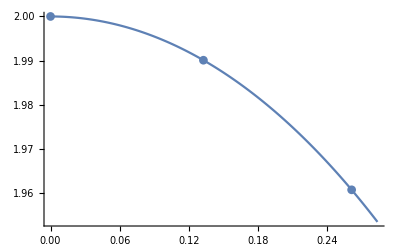

```mathematica
ModePlotOmega[2,0]
```

```mathematica
Options[ModeSolution]
```

{JacobianStep→-10,NoNegω→False,QNMPrecision→24,RadialCFDigits→8,RadialCFMinDepth→300,RadialDebug→0,RadialRelax→1,RCFPower→Null[],Rootϵ→Null[],SolutionDebug→0,SolutionIter→50,SolutionOscillate→10,SolutionSlow→10}

```mathematica
SelectMode[PolynomialMode]
```

Mode set to find Polynomial solutions

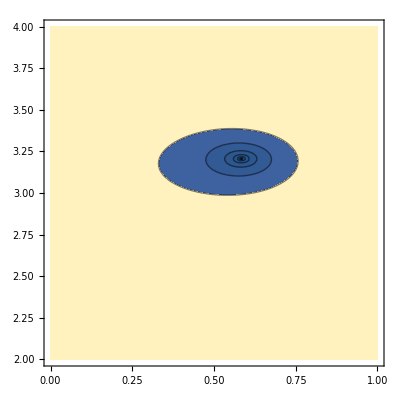

```mathematica
ContourPlot[Abs[PlotModeFunctionL[0,-2,0,51/100,1,ωr-ⅈ ωi,0,15]],{ωr,0,1},{ωi,2,4},Contours->{1/8,1/4,1/2,1,2,4,8,16,32,64}]
```

```mathematica
?PlotModeFunction
```

Arguments: n,s,m,a,Alm,ω,Nrcf,Nm
	 n -> Overtone level (integer).
	 s -> SpinWeight (integer).
	 m -> Azimuthal index (integer).
	 a -> Dimensionless spin parameter(rational or integer).
	 Alm -> Angular separation constant (integer).
	 Nrcf -> How deep into the continued fraction (integer).
	 Nm -> Number of azimuthal indecies(integer).

When in ContinuedFractionMode, package will require input for all the arguments and will use SelectMode
	 to replace ModeFunction with RadialCFRem.
When in PolynomialMode, n and Nrcf are not used in this plot function. Put dummy value in place.
PolynomialMode will use SelectMode to replace Modefunction with Starobinsky.

```mathematica
?ModeSolution
```

QNMSolution[n,s,l,m,a,ωg,Almg,ϵ,relax,Nrcf,Nm,ω0,Alm0,rl,rt] finds a solution of the coupled radial and angular Teukolsky equations with spin-weight s, 'magnetic' index m, and dimensionless angular momentum a.  ωg and Almg are initial guesses for the frequency and separation constant, which are assumed to be associated with azimuthal index l and overtone index n.

	The solution is found by iteration, calling AngularSpectralRoot and RadialLentzRoot until the magnitude of the change produced by either is less than 10^ϵ.  'relax' is an initial under-relaxation parameter used in updating the current guesses. For the radial equation, the continued fraction is truncated at the Nrcf^th term.  For the angular equation, Nm sets the size of the spectral approximation matrix.

	ω0, Alm0, rl, and rt are used to specify solution windows centered around the initial guesses ωg and Almg.  ω0 and Alm0 represent the prior solutions in a sequence of solutions.  |ω0-ωg| and |Alm0-Almg| set a length scale d for each solution.  The window for each solution is a portion of an anulus centered on the prior solution.  The difference between the inner and outer rings of the anulus is 2*rl*d with the guess solution centered between.  The width of the wedge is 2*rt*d along the outer ring.  Solutions falling outside the solution window for either quantity are rejected.  If rl=0 or rt=0, the solution is always accepted.

Options:
	 SolutionDebug→0 : Integer
		 Verbosity of debugging output for solutions iteration.  Increasing
		 value increases verbosity.
	 RadialDebug→0 : Integer
		 Verbosity of debugging output.  Increasing value increases verbosity.
	 RadialRelax→1: Rational(or Integer)
		 Under-relaxation parameter.
	 JacobianStep→-10
		 Log10 of relative step size used in numerical evaluation of the 
		 Jacobian in Newton's method.

```mathematica
?PlotModeFunction
```

Arguments: n,s,m,a,Alm,ω,Nrcf,Nm
	 n -> Overtone level (integer).
	 s -> SpinWeight (integer).
	 m -> Azimuthal index (integer).
	 a -> Dimensionless spin parameter(rational or integer).
	 Alm -> Angular separation constant (integer).
	 Nrcf -> How deep into the continued fraction (integer).
	 Nm -> Number of azimuthal indecies(integer).

When in ContinuedFractionMode, package will require input for all the arguments and will use SelectMode
	 to replace ModeFunction with RadialCFRem.
When in PolynomialMode, n and Nrcf are not used in this plot function. Put dummy value in place.
PolynomialMode will use SelectMode to replace Modefunction with Starobinsky.

```mathematica
SchwarzschildTTML[2,0,RadialDebug->4,SchDebug->1]
```

Computing (l=2,n=0)

RadialLentzStep :{KerrModes`Private`δωr→-9.99500374737656280568554×10^-6,KerrModes`Private`δωi→0.000999750149899958625930798} : {-0.576143985599936531025921-0.00576288000000000015423491 ⅈ,0}

δω=-9.99500374737656280568554×10^-6+0.000999750149899958625930798 ⅈ  root=0.576172806481592181039581

ω=4.99625262343801234499851×10^-9-2.00000024985009993123995 ⅈ

RadialLentzStep :{KerrModes`Private`δωr→-4.9962519992810206336147×10^-9,KerrModes`Private`δωi→2.49850084331214418590972×10^-7} : {-0.000143913666546010033345319-2.87784187061478967805879×10^-6 ⅈ,0}

δω=-4.9962519992810206336147×10^-9+2.49850084331214418590972×10^-7 ⅈ  root=0.000143942437774787012507994

Conv.Rate: 4000.80021491544868023167 : False

ω=6.24156991711383808045256×10^-16-2.00000000000001560002553 ⅈ

Set $MinPrecision =28

RadialLentzStep :{KerrModes`Private`δωr→-6.241569917113789396127541818×10^-16,KerrModes`Private`δωi→1.560002552656791373291584416×10^-14} : {-8.98561470330318828587217626×10^-12-3.595144272257598776511884402×10^-13 ⅈ,0}

δω=-6.241569917113789396127541818×10^-16+1.560002552656791373291584416×10^-14 ⅈ  root=8.992803913107519250534493049×10^-12

Conv.Rate: 1.600640036006678063732783896×10^7 : False

ω=4.868432501885096229986790674×10^-30-2. ⅈ

Set $MinPrecision =44

RadialLentzStep :{KerrModes`Private`δωr→-4.8684325018850962299867906736828033984999319×10^-30,KerrModes`Private`δωi→6.0742806119807339645384126163805259310871118×10^-29} : {-3.4987856325009027635741256671407633578783776×10^-26-2.8042171210858154284723914282116307745013191×10^-27 ⅈ,0}

δω=-4.8684325018850962299867906736828033984999319×10^-30+6.0742806119807339645384126163805259310871118×10^-29 ⅈ  root=3.5100053046707280435110922889030976789890763×10^-26

Conv.Rate: 2.5620485248671325973827021812564446137491955×10^14 : False

SetPrecision::precsm: Requested precision 24 is smaller than $MinPrecision. Using $MinPrecision instead.

KerrModes`Private`RadialLentzStep::increase: Excessive increase in Precision, Abort

$Aborted

```mathematica
$MinPrecision=24
```

24

```mathematica
SelectMode[PolynomialMode]
```

Mode set to find Polynomial solutions

```mathematica
Plot3D[Abs[PlotModeFunctionL[0,-2,1,50/100,1,ωr-ⅈ ωi,300,15]],{ωr,0,1},{ωi,1,2}]
```

-Graphics3D-

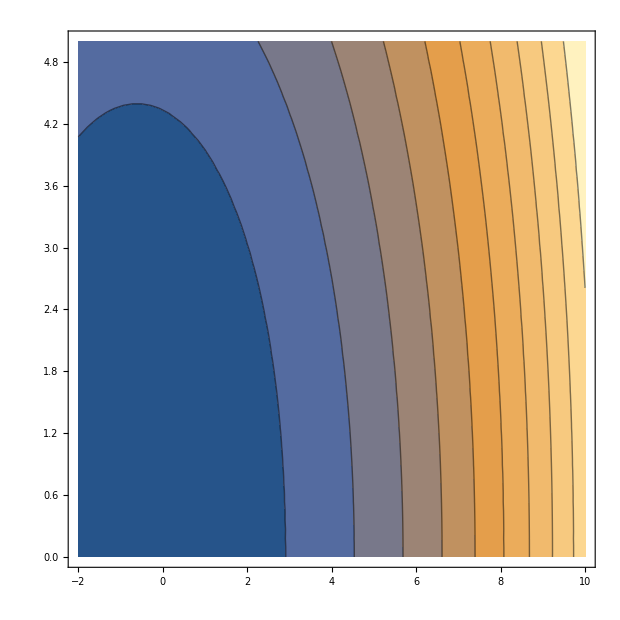

```mathematica
ContourPlot[Abs[PlotModeFunctionL[0,-2,-2,1/8,1,ωr-ⅈ ωi,3000,15]],{ωr,-2,10},{ωi,0,5},Contours->10]
```

```mathematica
Plot3D[{Re[PlotModeFunctionL[0,-2,-1,1/2,1,ωr-ⅈ ωi,3000,15]],Im[PlotModeFunctionL[0,-2,-1,1/2,1,ωr-ⅈ ωi,3000,15]]},{ωr,0,5},{ωi,0,5}]
```

-Graphics3D-

```mathematica
Plot3D[{Re[RadialCFRem[0,-2,0,0,4,ωr-ⅈ ωi,300][[1]]],Im[RadialCFRem[0,-2,0,0,4,ωr-ⅈ ωi,300][[1]]]},{ωr,0,4},{ωi,0,4}]
```

-Graphics3D-

```mathematica
RadialCFRem[0,-2,0,0,10,-ⅈ 10,2]
```

RadialCFRem[0,-2,0,0,10,-10 ⅈ,2]

```mathematica
SchwarzschildTTML[2,0,RadialDebug->1,SchDebug->0]
```

Computing (l=2,n=0)

Have made it into RadialCFRem

Have made it into RadialCFRem

Have made it into RadialCFRem

«17 more identical outputs»

KerrModes`Private`RadialLentzStep::increase: Excessive increase in Precision, Abort

$Aborted

```mathematica
?SchwarzschildTTML
```

SchwarzschildTTML[l,n] computes the Quasi-Normal Mode solutions for overtone n of mode l.  The mode is computed to an accuracy of 10^-14.  For given 'l', if solutions with overtones (n-1) and (n-2) have not been computed, then the routine is recersively called for overtone '(n-1).  If no solutions exist for mode l, then the first two overtones of (l-1) and (l-2) are used to extrapolate initial guesses for these modes.

Options:
	 SpinWeight→Null : -2,-1,0
		 The spin weight must be set via a call to SetSpinWeight before any KerrTTML
		 function call.
	 ModePrecision→24
	 JacobianStep→-10
		 The radial solver make use of numerical derivatives.  The relative step size
		 is set to 10^JacobianStep.
	 RadialCFMinDepth→300
		 The minimum value for the Radial Continued Fraction Depth.
	 RadialCFDepth→1
		 The initial Radial Continued Fraction Depth is usually taken from the prior 
		 solution in the sequence.  Fractional values reduce this initial value by that
		 fraction.  Integer values larger than RadialCFMinDepth are used as the new
		  initial value.
	 RadialRelax→1
		 Initial under-relaxation parameter used in Radial Newton iterations.
	 Rootϵ→-14
		 10^Rootϵ is the maximum allowed magnitude for the Radial Continued Fraction.
	 SchDebug→0 : 0,1,2,3,...
		 'Verbosity' level during the Schwarzschile iterations.
	 RadialDebug→0 : 0,1,2,3,...
		 'Verbosity' level during the Radial Newton iterations.